```mathematica
(* set options for plots *)
SetOptions[{Plot,ListPlot,Histogram},PlotRange->All,LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameStyle->Directive[Black],Frame->True,ImageSize->400];

(* set working directory *)
SetDirectory[NotebookDirectory[]];

(* default Mathematica colour scheme for plots *)
colors=ColorData[97,"ColorList"];

(* codes for colours, e.g. colors[[1]] etc *)
Grid[{Range[Length[colors]],colors}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

## Transcription model

### Model parameters

```mathematica
(* forward rates Subscript[k, 1],...,Subscript[k, 10] *)
kp=Table[0,{i,1,10}];

(* backward rates Subscript[k, -1],...,Subscript[k, -9] *)
km=Table[0,{i,1,9}];

(* promoter on rate [1/min] *)
(* source: Mammalian genes are transcribed with widely different bursting kineticshttps://doi.org/10.1126/science.1198817Nonehttps://doi.org/10.1126/science.1198817HyperlinkActionRecycledHyperlinkActive *)
kp[[1]]=0.04;

(* promoter off rate [1/min] *)
(* source: Mammalian genes are transcribed with widely different bursting kineticshttps://doi.org/10.1126/science.1198817Nonehttps://doi.org/10.1126/science.1198817HyperlinkActionRecycledHyperlinkActive *)
km[[1]]=0.53;

(* binding rate of TFIID [1/min] *)
(* source: Kinetic analysis of yeast TFIID-TATA box complex formation suggests a multi-step pathwayhttps://doi.org/10.1016/S0021-9258(19)49944-4Nonehttps://doi.org/10.1016/S0021-9258(19)49944-4HyperlinkActionRecycledHyperlinkActive *)
(* initial value: association time 1.1 min *)
kp[[2]]=1/1.1;

(* unbinding rate of TFIID [1/min] *)
(* source: Kinetic analysis of yeast TFIID-TATA box complex formation suggests a multi-step pathwayhttps://doi.org/10.1016/S0021-9258(19)49944-4Nonehttps://doi.org/10.1016/S0021-9258(19)49944-4HyperlinkActionRecycledHyperlinkActive *)
(* dinitial value: dissociation time 130 min *)
km[[2]]=1/130.0;

(* binding rate of TFIIA [1/min] *)
(* source: Rapid dynamics of general transcription factor TFIIB binding...http://genesdev.cshlp.org/content/30/18/2106.fullNonehttp://genesdev.cshlp.org/content/30/18/2106.fullHyperlinkActionRecycledHyperlinkActive *)
(* initial value: 20 s after TFIID *)
kp[[3]]=1/(20.0/60);

(* unbinding rate of TFIIA [1/min] *)
(* source: Dynamic interplay of TFIIA,TBP and TATA DNAhttps://doi.org/10.1006/jmbi.1997.1152Nonehttps://doi.org/10.1006/jmbi.1997.1152HyperlinkActionRecycledHyperlinkActive *)
(* initial value: dissociation time 8-49 min *)
km[[3]]=1/8.0;

(* binding rate of TFIIB [1/min] *)
(* source: Rapid dynamics of general transcription factor TFIIB binding...http://genesdev.cshlp.org/content/30/18/2106.fullNonehttp://genesdev.cshlp.org/content/30/18/2106.fullHyperlinkActionRecycledHyperlinkActive *)
(* initial value: association time 3.2 s *)
kp[[4]]=1/(3.2/60);

(* unbinding rate of TFIIB [1/min] *)
(* source: Rapid dynamics of general transcription factor TFIIB binding...http://genesdev.cshlp.org/content/30/18/2106.fullNonehttp://genesdev.cshlp.org/content/30/18/2106.fullHyperlinkActionRecycledHyperlinkActive *)
(* initial value: dissociation time 1.5 s *)
km[[4]]=1/(20*1.5/60);

(* binding of TFIIF and RNA polymerase [1/min] *)
(* source: Dynamics of RNA polymerase II and elongation factor Spt4/5 recruitment...https://doi.org/10.1073/pnas.2011224117Nonehttps://doi.org/10.1073/pnas.2011224117HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 2.3*10^-3 s^-1 *)
kp[[5]]=30*2.3*10^-3*60;

(* unbinding of TFIIF and RNA polymerase [1/min] *)
(* source: Dynamics of RNA polymerase II and elongation factor Spt4/5 recruitment...https://doi.org/10.1073/pnas.2011224117Nonehttps://doi.org/10.1073/pnas.2011224117HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 3.0*10^-3 s^-1 *)
km[[5]]=3.0*10^-3*60;

(* binding of TFIIE [1/min] *)
(* source: Single-molecule studies reveal branched pathways...https://doi.org/10.1016/j.molcel.2021.07.025Nonehttps://doi.org/10.1016/j.molcel.2021.07.025HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 1.7*10^-2 s^-1 *)
kp[[6]]=1.7*10^-2*60;

(* unbinding of TFIIE [1/min] *)
(* source: Single-molecule studies reveal branched pathways...https://doi.org/10.1016/j.molcel.2021.07.025Nonehttps://doi.org/10.1016/j.molcel.2021.07.025HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 5*10^-2 s^-1 *)
km[[6]]=5*10^-2*60;

(* binding of TFIIH [1/min] *)
(* source: Single-molecule studies reveal branched pathways...https://doi.org/10.1016/j.molcel.2021.07.025Nonehttps://doi.org/10.1016/j.molcel.2021.07.025HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 5*10^-2 s^-1 *)
kp[[7]]=5*10^-2*60;

(* unbinding of TFIIH [1/min] *)
(* source: Single-molecule studies reveal branched pathways...https://doi.org/10.1016/j.molcel.2021.07.025Nonehttps://doi.org/10.1016/j.molcel.2021.07.025HyperlinkActionRecycledHyperlinkActive *)
(* initial value: dissociation time in minutes *)
km[[7]]=1/5.0;

(* closed to open PIC [1/min] *)
(* source: Mechanism of Transcription Initiation at an Activator-Dependent Promoter...https://doi.org/10.1016/j.cell.2012.01.018Nonehttps://doi.org/10.1016/j.cell.2012.01.018HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 1.9*10^-3 s^-1 *)
kp[[8]]=30*1.9*10^-3*60;

(* open to closed PIC [1/min] *)
(* source: Mechanism of Transcription Initiation at an Activator-Dependent Promoter...https://doi.org/10.1016/j.cell.2012.01.018Nonehttps://doi.org/10.1016/j.cell.2012.01.018HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 1.1*10^-4 s^-1 *)
km[[8]]=1.1*10^-4*60;

(* open PIC to elongation [1/min] *)
(* source: Mechanism of Transcription Initiation at an Activator-Dependent Promoter...https://doi.org/10.1016/j.cell.2012.01.018Nonehttps://doi.org/10.1016/j.cell.2012.01.018HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 0.17 s^-1 *)
kp[[9]]=0.17*60;
km[[9]]=0.0;

(* escape from promotor proximal pausing *)
(* source: Kinetics of promoter pol ii on hsp70 reveal stable pausing and key insights into its regulationhttps://doi.org/10.1101/gad.231886.113Nonehttps://doi.org/10.1101/gad.231886.113HyperlinkActionRecycledHyperlinkActive *)
(* initial value: 5 min *)
kp[[10]]=1/0.5;

(* RNA polymerase II elongation speed [kb/min]*)
(* source: In vivo dynamics of RNA polymerase II transcriptionhttps://doi.org/10.1038/nsmb1280Nonehttps://doi.org/10.1038/nsmb1280HyperlinkActionRecycledHyperlinkActive *)
vRNAP=4.3;

(* median human gene length [kb] *)
(* source: NCBIhttps://www.ncbi.nlm.nih.gov/gene/18810Nonehttps://www.ncbi.nlm.nih.gov/gene/18810HyperlinkActionRecycledHyperlinkActive *)
geneL=60.404;

(* measurement time [min] *)
T=SetPrecision[geneL/vRNAP,200*$MachinePrecision];

(* reinitiation to state K *)
K=2;

(* write everything in nice tables *)
forwardrates=Grid[{{"k_1 [s^-1]","k_2 [1/min]","k_3 [1/min]","k_4 [1/min]","k_5 [1/min]","k_6 [1/min]","k_7 [1/min]","k_8 [1/min]","k_9 [1/min]","k_10 [1/min]"},kp},Frame->All,Background->{None,{LightGreen,None},None}];
backwardrates=Grid[{{"k_-1 [1/min]","k_-2 [1/min]","k_-3 [1/min]","k_-4 [1/min]","k_-5 [1/min]","k_-6 [1/min]","k_-7 [1/min]","k_-8 [min^-1 ]","k_-9 [1/min]"},km},Frame->All,Background->{None,{LightRed,None},None}];
forwardrates
backwardrates
Grid[{{"Elongation time [min]","State after reinitiation"},{N[T],K}},Frame->All,Background->{None,{LightBlue,None},None}]
```

k_1 [s^-1] | k_2 [1/min] | k_3 [1/min] | k_4 [1/min] | k_5 [1/min] | k_6 [1/min] | k_7 [1/min] | k_8 [1/min] | k_9 [1/min] | k_10 [1/min]
0.04 | 0.909091 | 3. | 18.75 | 4.14 | 1.02 | 3 | 3.42 | 10.2 | 2.

k_-1 [1/min] | k_-2 [1/min] | k_-3 [1/min] | k_-4 [1/min] | k_-5 [1/min] | k_-6 [1/min] | k_-7 [1/min] | k_-8 [min^-1 ] | k_-9 [1/min]
0.53 | 0.00769231 | 0.125 | 2. | 0.18 | 3 | 0.2 | 0.0066 | 0.

Elongation time [min] | State after reinitiation
14.0474 | 2

### Distribution of the waiting time between two initiations

```mathematica
(* set precision of all the rates *)
dummy=SetPrecision[kp,200*$MachinePrecision];
kp=dummy;
dummy=SetPrecision[km,200*$MachinePrecision];
km=dummy;

(* matrix A, above diagonal *)
c=Table[km[[i]],{i,1,9}];

(* matrix A, diagonal *)
b=Prepend[Table[-(kp[[i]]+km[[i-1]]),{i,2,10}],-kp[[1]]];

(* matrix A, below diagonal *)
a=Table[kp[[i]],{i,1,9}]; 

(* y functions *)
y[11][s_]:=1;
y[10][s_]:=s-b[[10]];
y[9][s_]:=(s-b[[9]])*y[10][s]-a[[9]]*c[[9]];
y[8][s_]:=(s-b[[8]])*y[9][s]-a[[8]]*c[[8]]*y[10][s];
y[7][s_]:=(s-b[[7]])*y[8][s]-a[[7]]*c[[7]]*y[9][s];
y[6][s_]:=(s-b[[6]])*y[7][s]-a[[6]]*c[[6]]*y[8][s];
y[5][s_]:=(s-b[[5]])*y[6][s]-a[[5]]*c[[5]]*y[7][s];
y[4][s_]:=(s-b[[4]])*y[5][s]-a[[4]]*c[[4]]*y[6][s];
y[3][s_]:=(s-b[[3]])*y[4][s]-a[[3]]*c[[3]]*y[5][s];
y[2][s_]:=(s-b[[2]])*y[3][s]-a[[2]]*c[[2]]*y[4][s];
y[1][s_]:=(s-b[[1]])*y[2][s]-a[[1]]*c[[1]]*y[3][s];

(* z functions *)
z[0][s_]:=1;
z[1][s_]:=s-b[[1]];
z[2][s_]:=(s-b[[2]])*z[1][s]-a[[1]]*c[[1]];
z[3][s_]:=(s-b[[3]])*z[2][s]-a[[2]]*c[[2]]*z[1][s];
z[4][s_]:=(s-b[[4]])*z[3][s]-a[[3]]*c[[3]]*z[2][s];
z[5][s_]:=(s-b[[5]])*z[4][s]-a[[4]]*c[[4]]*z[3][s];
z[6][s_]:=(s-b[[6]])*z[5][s]-a[[5]]*c[[5]]*z[4][s];
z[7][s_]:=(s-b[[7]])*z[6][s]-a[[6]]*c[[6]]*z[5][s];
z[8][s_]:=(s-b[[8]])*z[7][s]-a[[7]]*c[[7]]*z[6][s];
z[9][s_]:=(s-b[[9]])*z[8][s]-a[[8]]*c[[8]]*z[7][s];
z[10][s_]:=(s-b[[10]])*z[9][s]-a[[9]]*c[[9]]*z[8][s]

(* K=1 *)
f1[s_]:=kp[[10]]*((-Product[-kp[[i]],{i,1,9}]*(1/y[2][s]))/((s-b[[1]])-a[[1]]*c[[1]]*(y[3][s]/y[2][s])));

(* K=2,...,9 *)
fK[s_]:=kp[[10]]*(((-1)^(10-K)*Product[-kp[[K-1+i]],{i,1,10-K}]*(1/y[K+1][s]))/((s-b[[K]])-a[[K-1]]*c[[K-1]]*(z[K-2][s]/z[K-1][s])-a[[K]]*c[[K]]*(y[K+2][s]/y[K+1][s])));

(* K=10 *)
f10[s_]:=kp[[10]]*(1/((s-b[[10]])-a[[9]]*c[[9]]*(z[8][s]/z[9][s])));

(* Laplace transform of the waiting time distribution *)
SuperStar[g][s_]:=If[K==1,f1[s],If[K==10,f10[s],fK[s]]]
P1=CoefficientList[Expand[Numerator[Factor[SuperStar[g][s]]]],s];
degP1=Length[P1]-1;
P2=CoefficientList[Expand[Denominator[Factor[SuperStar[g][s]]]],s];
degP2=Length[P2]-1;
SuperStar[f][s_]:=(P1[[1]]+∑_(n=1)^degP1 P1[[n+1]]*s^n)/(P2[[1]]+∑_(n=1)^degP2 P2[[n+1]]*s^n);

(* find the mean initiation time [s]*)
μ=-D[SuperStar[g][s],{s,1}]/.s->0;

(* find the standard deviation of the waiting time [s] *)
σ=√((D[SuperStar[g][s],{s,2}]/.s->0)-μ*μ);

(* find the Fano factor *)
FFwt=σ^2/μ;

(* write everything in a nice table *)
Grid[{{"Mean initiation time [min]","Standard deviation [min]","Fano factor"},{N[μ],N[σ],N[FFwt]}},Frame->All,Background->{None,{LightOrange,None},None}]
```

Mean initiation time [min] | Standard deviation [min] | Fano factor
19.732 | 31.3632 | 49.8506

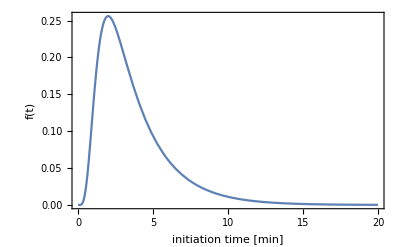

```mathematica
(* plot the waiting time distribution *)
f[t_]:=InverseLaplaceTransform[SuperStar[f][s],s,t]
plot1=Plot[f[SetPrecision[t,100*$MachinePrecision]],{t,0,20},FrameLabel->{"initiation time [min]","f(t)"}]
```

```mathematica
(* export waiting time distribution to a file *)
dataf=Table[{0.2*t,N[f[SetPrecision[0.2*t,100*$MachinePrecision]]]},{t,1,100}];
```

```mathematica
Export["wt-dist-Plec-K4-exact.csv",dataf]
```

wt-dist-Plec-K4-exact.csv

### Nascent RNA distribution (stationary state)

```mathematica
P1=CoefficientList[Expand[Numerator[Factor[SuperStar[g][s]]]],s];
degP1=Length[P1]-1;
P2=CoefficientList[Expand[Denominator[Factor[SuperStar[g][s]]]],s];
degP2=Length[P2]-1;

(* Laplace transform of the waiting time distribution *)
SuperStar[f][s_]:=(P1[[1]]+∑_(n=1)^degP1 P1[[n+1]]*s^n)/(P2[[1]]+∑_(n=1)^degP2 P2[[n+1]]*s^n);

(* h[s]=1-f^*[s] *)
SuperStar[h][s_]:=(∑_(n=1)^degP1 (P2[[n+1]]-P1[[n+1]])*s^n+∑_(n=degP1+1)^degP2 P2[[n+1]]*s^n)/(P2[[1]]+∑_(n=1)^degP2 P2[[n+1]]*s^n);

(* find mean of the nascent RNA *)
Subscript[μ, N]=T/μ; 

(* find variance of the nascent RNA *)
VarN=Re[InverseLaplaceTransform[(1+SuperStar[f][s])/(μ*s^2*SuperStar[h][s]),s,T]-Subscript[μ, N]*Subscript[μ, N]];

(* find standard deviation of the nascent RNA*)
Subscript[σ, N]=√VarN;

(* find the Fano factor*)
FFN=VarN/Subscript[μ, N];

(* write everything in a nice table *)
Grid[{{"mean nascent RNA","standard deviation","Fano factor"},{N[Subscript[μ, N]],N[Subscript[σ, N]],N[FFN]}},Frame->All,Background->{None,{LightMagenta,None},None}]
```

mean nascent RNA | standard deviation | Fano factor
3.81361 | 1.32185 | 0.458172

```mathematica
(* Laplace transform of the nascent RNA distribution *)
SuperStar[P][n_,s_]:=If[n==0,1/s-(SuperStar[h][s])/(μ*s^2),1/μ*((SuperStar[h][s])/s)^2*(SuperStar[f][s])^(n-1)]

(* nascent RNA distribution *)
P=Table[{n,N[InverseLaplaceTransform[SuperStar[P][n,s],s,T]]},{n,0,10}]

(* check the normalisation *)
Total[P[[All,2]]]
```

{{0,0.00297978},{1,0.0301028},{2,0.122939},{3,0.255152},{4,0.294316},{5,0.196261},{6,0.0772292},{7,0.0181852},{8,0.00259511},{9,0.000227495},{10,0.0000124354}}

1.

```mathematica
(* plot the nascent RNA distribution *)
plot2=ListPlot[P,PlotMarkers->Automatic,FrameLabel->{"nascent RNA number n","P(N=n)"}]
```

```mathematica
(* export the nascent RNA distribution to a file *)
Export["nascent-RNA-dist-Plec-K4-exact.csv",P]
```

nascent-RNA-dist-Plec-K4-exact.csv

### Sensitivity analysis of the Fano factor of the nascent RNA distribution

```mathematica
(* set precision of all the rates *)
dummy=SetPrecision[kp,200*$MachinePrecision];
kp=dummy;
dummy=SetPrecision[km,200*$MachinePrecision];
km=dummy;

kpvar={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10};
kmvar={y1,y2,y3,y4,y5,y6,y7,y8,y9};

(* matrix A, above diagonal *)
c=Table[kmvar[[i]],{i,1,9}];

(* matrix A, diagonal *)
b=Prepend[Table[-(kpvar[[i]]+kmvar[[i-1]]),{i,2,10}],-kpvar[[1]]];

(* matrix A, below diagonal *)
a=Table[kpvar[[i]],{i,1,9}]; 

(* y functions *)
y[11][s_]:=1;
y[10][s_]:=s-b[[10]];
y[9][s_]:=(s-b[[9]])*y[10][s]-a[[9]]*c[[9]];
y[8][s_]:=(s-b[[8]])*y[9][s]-a[[8]]*c[[8]]*y[10][s];
y[7][s_]:=(s-b[[7]])*y[8][s]-a[[7]]*c[[7]]*y[9][s];
y[6][s_]:=(s-b[[6]])*y[7][s]-a[[6]]*c[[6]]*y[8][s];
y[5][s_]:=(s-b[[5]])*y[6][s]-a[[5]]*c[[5]]*y[7][s];
y[4][s_]:=(s-b[[4]])*y[5][s]-a[[4]]*c[[4]]*y[6][s];
y[3][s_]:=(s-b[[3]])*y[4][s]-a[[3]]*c[[3]]*y[5][s];
y[2][s_]:=(s-b[[2]])*y[3][s]-a[[2]]*c[[2]]*y[4][s];
y[1][s_]:=(s-b[[1]])*y[2][s]-a[[1]]*c[[1]]*y[3][s];

(* z functions *)
z[0][s_]:=1;
z[1][s_]:=s-b[[1]];
z[2][s_]:=(s-b[[2]])*z[1][s]-a[[1]]*c[[1]];
z[3][s_]:=(s-b[[3]])*z[2][s]-a[[2]]*c[[2]]*z[1][s];
z[4][s_]:=(s-b[[4]])*z[3][s]-a[[3]]*c[[3]]*z[2][s];
z[5][s_]:=(s-b[[5]])*z[4][s]-a[[4]]*c[[4]]*z[3][s];
z[6][s_]:=(s-b[[6]])*z[5][s]-a[[5]]*c[[5]]*z[4][s];
z[7][s_]:=(s-b[[7]])*z[6][s]-a[[6]]*c[[6]]*z[5][s];
z[8][s_]:=(s-b[[8]])*z[7][s]-a[[7]]*c[[7]]*z[6][s];
z[9][s_]:=(s-b[[9]])*z[8][s]-a[[8]]*c[[8]]*z[7][s];
z[10][s_]:=(s-b[[10]])*z[9][s]-a[[9]]*c[[9]]*z[8][s];

(* K=1 *)
f1[s_]:=kpvar[[10]]*(-Product[-kpvar[[i]],{i,1,9}]*1/(y[2][s]))/((s-b[[1]])-a[[1]]*c[[1]]*(y[3][s])/(y[2][s]));

(* K=2,...,9 *)
fK[s_]:=kpvar[[10]]*((-1)^(10-K)*Product[-kpvar[[K-1+i]],{i,1,10-K}]*1/(y[K+1][s]))/((s-b[[K]])-a[[K-1]]*c[[K-1]]*(z[K-2][s])/(z[K-1][s])-a[[K]]*c[[K]]*(y[K+2][s])/(y[K+1][s]));

(* K=10 *)
f10[s_]:=kpvar[[10]]*1/((s-b[[10]])-a[[9]]*c[[9]]*(z[8][s])/(z[9][s]));

(* Laplace transform of the waiting time distribution *)
SuperStar[g][s_]:=If[K==1,f1[s],If[K==10,f10[s],fK[s]]]
P1=CoefficientList[Expand[Numerator[Factor[SuperStar[g][s]]]],s];
degP1=Length[P1]-1;
P2=CoefficientList[Expand[Denominator[Factor[SuperStar[g][s]]]],s];
degP2=Length[P2]-1;
SuperStar[f][s_]:=(P1[[1]]+∑_(n=1)^degP1 P1[[n+1]]*s^n)/(P2[[1]]+∑_(n=1)^degP2 P2[[n+1]]*s^n);

(* h[s]=1-f^*[s] *)
SuperStar[h][s_]:=(∑_(n=1)^degP1 (P2[[n+1]]-P1[[n+1]])*s^n+∑_(n=degP1+1)^degP2 P2[[n+1]]*s^n)/(∑_(n=0)^degP2 P2[[n+1]]*s^n);
```

```mathematica
(* find the mean initiation time [s]*)
μ=-D[SuperStar[f][s],{s,1}]/.{s->0,x1->kp[[1]],y1->km[[1]],x2->kp[[2]],y2->km[[2]],x3->kp[[3]],y3->km[[3]],x4->kp[[4]],y4->km[[4]],x5->kp[[5]],y5->km[[5]],x6->kp[[6]],y6->km[[6]],x7->kp[[7]],y7->km[[7]],x8->kp[[8]],y8->km[[8]],x9->kp[[9]],y9->km[[9]],x10->kp[[10]]};

(* find the mean of the nascent RNA *)
Subscript[μ, N]=T/μ;

(* find the variance of the nascent RNA *)
VarN=Re[InverseLaplaceTransform[(1+SuperStar[f][s])/(μ*s^2*SuperStar[h][s])/.{x1->kp[[1]],y1->km[[1]],x2->kp[[2]],y2->km[[2]],x3->kp[[3]],y3->km[[3]],x4->kp[[4]],y4->km[[4]],x5->kp[[5]],y5->km[[5]],x6->kp[[6]],y6->km[[6]],x7->kp[[7]],y7->km[[7]],x8->kp[[8]],y8->km[[8]],x9->kp[[9]],y9->km[[9]],x10->kp[[10]]},s,T]-Subscript[μ, N]*Subscript[μ, N]];

(* find the standard deviation of the nascent RNA *)
Subscript[σ, N]=√VarN;

(* find the Fano factor *)
FFN=VarN/Subscript[μ, N];

(* write everything in a nice table *)
Grid[{{"mean nascent RNA","standard deviation","Fano factor"},{N[Subscript[μ, N]],N[Subscript[σ, N]],N[FFN]}},Frame->All,Background->{None,{LightMagenta,None},None}]
```

mean nascent RNA | standard deviation | Fano factor
0.711911 | 1.05026 | 1.54941

```mathematica
(* a list to store the relative sensitivity coefficient in *)
Sdata={};

(* find the sensitivity coefficient for the forward rates *)
Do[
D1=(-Subscript[μ, N]*Subscript[μ, N])/T*(D[-D[SuperStar[f][s],{s,1}]/.s->0,{kpvar[[i]],1}]/.{x1->kp[[1]],y1->km[[1]],x2->kp[[2]],y2->km[[2]],x3->kp[[3]],y3->km[[3]],x4->kp[[4]],y4->km[[4]],x5->kp[[5]],y5->km[[5]],x6->kp[[6]],y6->km[[6]],x7->kp[[7]],y7->km[[7]],x8->kp[[8]],y8->km[[8]],x9->kp[[9]],y9->km[[9]],x10->kp[[10]]});
D2=Re[InverseLaplaceTransform[D[(1+SuperStar[f][s])/(μ*s^2*SuperStar[h][s]),{kpvar[[i]],1}]/.{x1->kp[[1]],y1->km[[1]],x2->kp[[2]],y2->km[[2]],x3->kp[[3]],y3->km[[3]],x4->kp[[4]],y4->km[[4]],x5->kp[[5]],y5->km[[5]],x6->kp[[6]],y6->km[[6]],x7->kp[[7]],y7->km[[7]],x8->kp[[8]],y8->km[[8]],x9->kp[[9]],y9->km[[9]],x10->kp[[10]]},s,T]];

(* relative sensitivity coefficient, FF *)
S=kp[[i]]/FFN*(D2/Subscript[μ, N]-(VarN/(Subscript[μ, N]*Subscript[μ, N])+2)*D1);
dummy=Sdata;
Sdata=Append[dummy,N[S]],{i,1,10}]

(* find the sensitivity coefficient for the backward rates *)
Do[
D1=(-Subscript[μ, N]*Subscript[μ, N])/T*(D[-D[SuperStar[f][s],{s,1}]/.s->0,{kmvar[[i]],1}]/.{x1->kp[[1]],y1->km[[1]],x2->kp[[2]],y2->km[[2]],x3->kp[[3]],y3->km[[3]],x4->kp[[4]],y4->km[[4]],x5->kp[[5]],y5->km[[5]],x6->kp[[6]],y6->km[[6]],x7->kp[[7]],y7->km[[7]],x8->kp[[8]],y8->km[[8]],x9->kp[[9]],y9->km[[9]],x10->kp[[10]]});
D2=Re[InverseLaplaceTransform[D[(1+SuperStar[f][s])/(μ*s^2*SuperStar[h][s]),{kmvar[[i]],1}]/.{x1->kp[[1]],y1->km[[1]],x2->kp[[2]],y2->km[[2]],x3->kp[[3]],y3->km[[3]],x4->kp[[4]],y4->km[[4]],x5->kp[[5]],y5->km[[5]],x6->kp[[6]],y6->km[[6]],x7->kp[[7]],y7->km[[7]],x8->kp[[8]],y8->km[[8]],x9->kp[[9]],y9->km[[9]],x10->kp[[10]]},s,T]];

(* relative sensitivity coefficient, FF *)
S=km[[i]]/FFN*(D2/Subscript[μ, N]-(VarN/(Subscript[μ, N]*Subscript[μ, N])+2)*D1);
dummy=Sdata;
Sdata=Append[dummy,N[S]],{i,1,8}]
Sdata
```

{-1.37623,-1.06863,0.0269745,0.0079388,0.0285289,0.115734,0.0806877,0.0298612,0.00913118,0.0428899,1.0944,0.00282438,-0.000265632,-0.00280096,-0.00488994,-0.0561572,-0.00408187,-0.0000188919}

```mathematica
Sdata2=Transpose[{Join[Range[10],-Range[8]],Sdata}]
```

{{1,-1.37623},{2,-1.06863},{3,0.0269745},{4,0.0079388},{5,0.0285289},{6,0.115734},{7,0.0806877},{8,0.0298612},{9,0.00913118},{10,0.0428899},{-1,1.0944},{-2,0.00282438},{-3,-0.000265632},{-4,-0.00280096},{-5,-0.00488994},{-6,-0.0561572},{-7,-0.00408187},{-8,-0.0000188919}}

```mathematica
Sdata3={Sdata2[[1]],Sdata2[[11]],Sdata2[[2]],Sdata2[[12]],Sdata2[[3]],Sdata2[[13]],Sdata2[[4]],Sdata2[[14]],Sdata2[[5]],Sdata2[[15]],Sdata2[[6]],Sdata2[[16]],Sdata2[[7]],Sdata2[[17]],Sdata2[[8]],Sdata2[[18]],Sdata2[[9]],Sdata2[[10]]}
```

{{1,-1.37623},{-1,1.0944},{2,-1.06863},{-2,0.00282438},{3,0.0269745},{-3,-0.000265632},{4,0.0079388},{-4,-0.00280096},{5,0.0285289},{-5,-0.00488994},{6,0.115734},{-6,-0.0561572},{7,0.0806877},{-7,-0.00408187},{8,0.0298612},{-8,-0.0000188919},{9,0.00913118},{10,0.0428899}}

```mathematica
Export["sensitivity-FF-nascent-RNA-Plec-K2.csv",Sdata3]
```

sensitivity-FF-nascent-RNA-Plec-K2.csv